```mathematica
(*a set of standard units that are used when not specified*)standardUnits={"Seconds","Meters","Kilograms","Kelvins","KelvinsDifference","Amperes","Candelas","Moles","Radians"};
standardUnitDimensions=UnitDimensions[#][[1,1]]&/@standardUnits;

makeUnitSystem::overcomplete="The unit system `1` is overcomplete. Please remove some unit.";
makeUnitSystem[]=Thread[standardUnitDimensions->standardUnits];
makeUnitSystem[L_List]:=Module[{M,n,u},(*convert the desired unit system to base units*)M=Lookup[#,standardUnitDimensions,0]&/@Apply[Rule,UnitDimensions/@L,{2}];
If[MatrixRank[M]<Length[L],Message[makeUnitSystem::overcomplete,L];
Return[$Failed]];
(*check which base units cannot be expressed in this system*)n=Position[Diagonal[PseudoInverse[M].M],Except[1],{1},Heads->False];
(*extend the unit system if necessary*)If[Length[n]>0,Return[makeUnitSystem[Append[L,standardUnits[[n[[1,1]]]]]]]];
(*find the compound units that represent the base units*)u=Times@@@Transpose[L^Transpose[PseudoInverse[M]]];
(*return replacement list*)Thread[standardUnitDimensions->u]]

unitConvert[x_Quantity,unitSystem_/;VectorQ[unitSystem,Head[#]===Rule&]]:=UnitConvert[x,Times@@Power@@@(UnitDimensions[x]/. unitSystem)]
```

```mathematica
unitsystem=makeUnitSystem[{Quantity[1.15*1064,"Nanometers"],Quantity["PlanckConstant"],ChemicalFormula["NaCs"]["MolecularMass"]}];
```

Replacement of the constants used in the experiment

```mathematica
units={nm->Quantity["Nanometers"],um->Quantity["Micrometers"]};
fundamental={h->Quantity["PlanckConstant"],ℏ->Quantity["ReducedPlanckConstant"]};
```

```mathematica
rep=Association[m->ChemicalFormula["NaCs"]["MolecularMass"],U0->h  Quantity[1, "Megahertz"],W0->1.15 1064 nm,λ->1064 nm]/.units/.fundamental;
```

```mathematica
unitConvert[rep[[#]],unitsystem]&/@Range[Length[rep]]
```

{155.8952212 u,2.50606925×10^-6 h^2/(u nm^2),1223.6 nm,1064 nm}

```mathematica
rep[[4]]
```

1064 nm

```mathematica
unitConvert[Quantity[1,"Micrometers"],unitsystem]
```

1000 nm

Tweezer potential

```mathematica
z0=(π W0^2)/λ;
W=W0 √(1+(z/z0)^2);
intensity=2ϵ0 c U0/Re[α] (W0/W)^2 Exp[-(2 x^2)/W^2];

U=U0-1/(2ϵ0 c)Re[α]intensity/.z->0//.rep//N;
```

Trap frequency

```mathematica
ωx=ω/.Solve[(m ω^2==(2/x^2 Normal[Series[U/.z->0,{x,0,2}]])/.rep)&&ω>0,ω][[1]];
```

Eigenstates

```mathematica
ψn[n_]:=1/(√(2^n n!))((m ωx)/(π ℏ))^(1/4)Exp[-(m ωx x^2)/(2ℏ)]HermiteH[n,√((m ωx)/ℏ)x]//.rep
```

```mathematica
ψn[0]
```

2835.2 ⅇ^(-1.01497×10^14 x^2)

Schrodinger equation

```mathematica
SE=(ⅈ D[#,t]+ℏ/(2m)D[#,x,x]- (U +0.1U Cos[2π ωx t])/ℏ#)&[ψ[x,t]]==0/.rep//N
```

-9.48252×10^33 (6.62607×10^-28-6.62607×10^-28 2.71828^(-1.33583×10^12 x^2)+0.1 (6.62607×10^-28-6.62607×10^-28 2.71828^(-1.33583×10^12 x^2)) Cos[519586. t]) ψ[x,t]+(0.+1. ⅈ) ψ^(0,1)[x,t]+2.03687×10^-10 ψ^(2,0)[x,t]==0.

### test

```mathematica
xmax=500 10^-9;tmax=10^-4;
sol=NDSolve[{SE,ψ[x,0]==ψn[0],ψ[xmax,t]==0,ψ[-xmax,t]==0},ψ,{x,-xmax,xmax},{t,0,tmax}];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.0000881404.

NDSolve::eerr: Warning: scaled local spatial error estimate of 624.742 at t = 0.0000881404 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 465 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

```mathematica
solution=ψ/. sol[[1]];
```

```mathematica
Manipulate[Plot[Abs[solution[x,t]]^2,{x,-xmax,xmax},PlotRange->{0,2 Abs[solution[0,0]]^2},Filling->{1->Axis}],{t,0,tmax}]
```

InterpolatingFunction::dmval: Input value {-4.9998×10^-7,0.0000994} lies outside the range of data in the interpolating function. Extrapolation will be used.

Plot::plln: Limiting value -xmax in {x,-xmax,xmax} is not a machine-sized real number.

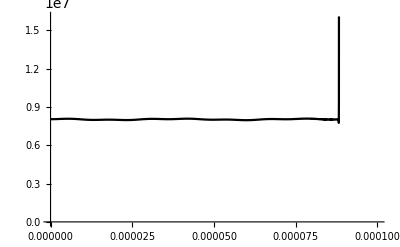

```mathematica
Plot[Abs[solution[0,t]]^2,{t,0,tmax},PlotRange->{0,2 Abs[solution[0,0]]^2},PlotStyle->Black]
```

## ND

```mathematica
ω=.;h=1;U0=4;ω0=1;ω[t_]=ω0+.01 Cos[1 ω0 t];m=1;a=1;
```

```mathematica
p=-ⅈ h/(2π) D[#,x]&;
(*H=(p[p[#]]/(2m)+U0(1-ⅇ^(-(1/2 m ω[t]^2)/U0 x^2))#)&;*)
H=(p[p[#]]/(2m)+1/2 m ω[t]^2 x^2#)&;
```

```mathematica
SE=ⅈ D[ψ[x,t],t]==(2π H[ψ[x,t]])/h;
```

```mathematica
ψeig[n_,x_]:=1/(√(2^n n!))((m a ω0)/(π ℏ))^(1/4)Exp[-(m a ω0 x^2)/(2ℏ)]HermiteH[n,√((m a ω0)/ℏ)x]
```

```mathematica
SE
```

ⅈ ψ^(0,1)[x,t]==4 (1-ⅇ^(-1/8 x^2 (1+0.01 Cos[t])^2)) ψ[x,t]-1/2 ψ^(2,0)[x,t]

```mathematica
xmax=10;tmax=200;
schrodingerEq=-(1/2) D[ψ[x,t],{x,2}]+(1/2) x^2 ψ[x,t]==I D[ψ[x,t],t];
ψinit[x_]:=(1/π)^(1/4) Exp[-1/2 (x-1)^2];
sol=NDSolve[{SE,ψ[x,0]==ψeig[0,x],ψ[xmax,t]==0,ψ[-xmax,t]==0},ψ,{x,-xmax,xmax},{t,0,tmax},PrecisionGoal->10];
solution=ψ/. sol[[1]];
```

```mathematica
Manipulate[Plot[{Abs[solution[x,0]]^2,Abs[solution[x,t]]^2,U0(1-ⅇ^(-1/2(m ω0^2)/U0 x^2)),1/2 m ω0^2 x^2},{x,-xmax,xmax},PlotRange->{0,1},PlotStyle->{Dotted,Blue,Red,Purple},Filling->{2->Axis}],{t,0,tmax}]
```

Plot::plln: Limiting value -xmax in {x,-xmax,xmax} is not a machine-sized real number.

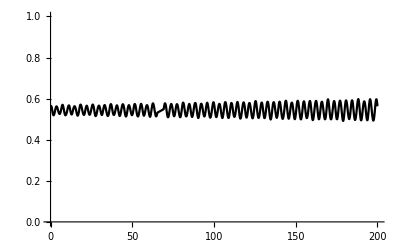

```mathematica
Plot[Abs[solution[0,t]]^2,{t,0,tmax},PlotRange->{0,1},PlotStyle->Black]
```